# Quantum harmonic oscillator with time-dependent frequency

## Modules

The following modules refer to the algebra
ℒ_n={h_1,..., h_n},
that fulfils the commutation rule
  [h_i,h_j]=i ℏ ∑_(𝓀=1)^𝓃 c_(i,j,k)h_k,
characterized by the structure constants c_(i,k,j.)

### LieGetMa

LieGetMa[c, J, vα] generates the M transormations of the for M_k=e^-Q_k for k=1,..., n and M_(n+1)=M_1... M_n is an n×n matrix and M is an n×n×n tensor corresponding to the structure constants c.

c     :  n×n×n tensor containing the structure constants,

J     :  n×n matrix, h'= Jh is a new representation of the ℒ_n,

vα: dimension n list vα={α_1,α_2,...,α_n} containing the transformation parameters for the U_A transformation.

```mathematica
LieGetMa[c_, J_, vα_] := Module[{dim, k, Q, M},
  dim = Dimensions[c][[1]];
  k = Dimensions[J][[1]];
  M = Table[0, {k1, 1, k + 1}, {k2, 1, dim}, {k3, 1, dim}];
  M[[k + 1]] = IdentityMatrix[k];
  Do[
   Q = Table[Sum[c[[k2, k3, k4]] J[[k1, k2]] vα[[k1]], {k2, 1, dim}], {k3, 1, dim}, {k4, 1, dim}];
   M[[k1]] = MatrixExp[-Q];
   M[[k + 1]] = M[[k + 1]].M[[k1]];
   , {k1, 1, k}];
  M
  ]
```

### LieGetNu

LieGetNu[M,J] generates the ν matrix where ν is an n×n matrix.

M  :  n×n×n tensor containing the transformation matrices,

J   : n×n matrix, h'= Jh is a new representation of the ℒ_n.

```mathematica
LieGetNu[M_,J_]:=Module[{dim,Mk,Ik,νt,νt1},
dim=Dimensions[M[[1]]][[1]];
Ik=Normal[SparseArray[{{1,1}->1},dim]];
νt1=Ik.J;
Do[
Mk=M[[k1]];
Ik=Normal[SparseArray[{{k1,k1}->1},dim]];
νt=νt1.Mk+Ik.J;
νt1=νt;
,{k1,2,dim}];
Transpose[νt]
]
```

### LieTrans

LieTrans[M,J,va,vα,k,t] transforms the coeficients I into va' under the k'th transformation U_k corresponding to the M_k matrix. Under this transformation the original Floquet operator H-p_t=va^⊤h-p_t is transformed into H'-p_t=U_k(H-p_t)U_k=va^⊤ M_k h-(α̇)_k h_k-p_t=(va')^⊤h-p_t where va'  is the new set of coefficients.

M    :  n×n×n tensor containing the transformation matrices,

J   :  n×n matrix, h'= Jh is a new representation of the ℒ_n,

va :dimension n list va={a_1,a_2,...,a_n} containing the coefficients of the original Floquet operator,

vα : dimension n list vα={α_1,α_2,...,α_n} containing the transformation parameters for the U_A transformation,

k     :  integer that tags the number of transformation to be used,

t     :  time parameter.

```mathematica
LieTrans[M_,J_,va_,vα_,k_,t_]:=va.M[[k]]-D[vα[[k]],t]J[[k]]
```

### LieGetu

LieGetu[M,J,va,vα,t]  transforms the original coefficients va into u under the complete transformation U_A corresponding to M_a=M_1 M_2...M_n.  Under this transformation the original Floquet operator H-p_t=(va.h-p)_t is transformed into H'-p_t=U_A(H-p_t)U_A=va^⊤M_a h-(α̇)^⊤ν^⊤h_k-p_t=u^⊤h-p_t.

M   : is an n×n×n tensor containing the transformation matrices,

J  : n×n matrix, h'= Jh is a new representation of the ℒ_n,

va: dimenison n list va={a_1,a_2,...,a_n} containing the coefficients of the original Floquet operator,

vα: dimension n list  containing the transformation parameters for the U_A transformation. The α parameters must be functions of the time parameter t.

t     :   time parameter.

```mathematica
LieGetu[M_,J_,va_,vα_,t_]:=Module[{k,vu,vw},
k=Dimensions[vα][[1]];
vu=va;
Do[
vw=LieTrans[M,J,vu,vα,k1,t];
vu=vw;
,{k1,1,k}];
vu
]
```

### LieGetDifEqLambda

LieGetDifEqLambda[J,νi,vα,vβ,λ,ci] calculates a list containing
the differential equations with respect to the auxiliary parameter
λ that connects the α and β parameters.

J      :  n×n matrix, h'= J.h is a new representation of the ℒ_n,

νi     : inverse of the n×n matrix ν calculated with LieGetNu[M,J],

vα : dimension n list vα={α_1,α_2,...,α_n} containing the transformation parameters for the U_A. The α parameters must be functions of the auxiliary parameter λ,

vβ :  dimension n list vβ={β_1,β_2,...,β_n} containing the transformation parameters for the U_B. The β parameters are NOT functions of the auxiliary parameter λ,

λ  : is the auxiliary parameter that helps relate the α and β transformation parameters.

ci : is a Boolean variable. If ci==True, the initial conditions α_1[0]==0, α_2[0]==0, ..., α_n[0]==0 is appended to the list of differential equations. If on ci==False then the output is just the list of differential equations,

λ  : is the auxiliary parameter that helps relate the α and β transformation parameters.

```mathematica
LieGetDifEqLambda[J_,νi_,vα_,vβ_,λ_,ci_]:=Module[{dim,v},
dim=Dimensions[vα][[1]];
v=νi.vβ;
If[ci==True,
Join[Table[D[vα[[k1]],λ]==v[[k1]],{k1,1,dim}],Table[(vα[[k1]]/.λ->0)==0,{k1,1,dim}]],
Table[D[vα[[k1]],λ]==v[[k1]],{k1,1,dim}]
]
]
```

### LieGetNAlpha

LieGetNAlpha[J,νi,vβ,m] numerically calculates the α parameters using Eq. (16).

J       :  n×n matrix, h'= J.h is a new representation of the ℒ_n,

νi     : inverse of the n×n matrix ν calculated with LieGetNu[M,J], νi must be a function of vα.

vα     :dimension n list vα={α_1,α_2,...,α_n} containing the transformation parameters for the U_B.

vβ     :dimension n list vβ={β_1,β_2,...,β_n} containing the transformation parameters for the U_B.

m     : number of iterations.

```mathematica
LieGetNAlpha[J_,νi_,vα_,vβ_,m_]:=Module[{dim,vα0,vα1,cond,νi0},
dim=Dimensions[vβ][[1]];
vα0=Table[0,{k1,1,dim}];
Do[
cond=Table[vα[[k1]]->vα0[[k1]],{k1,1,dim}];
νi0=νi/.cond;
vα1=1/m νi0.vβ+vα0;
vα0=vα1;
,{m1,0,m-1}];
vα1
]
```

## Main Program

### Definition of the structure constants c_(i,j,k)

The elements of this algebra are given by the operators h_1=x^2 , h_2=x p+p x, h_3=p^2. The following lines define the algebra dimension and the structure constants.

```mathematica
n=3;
d=Table[0,{k1,1,n},{k2,1,n},{k3,1,n}];
d[[1,2,3]]=2;
d[[2,1,3]]=-2;
d[[1,3,1]]=4;
d[[3,1,1]]=-4;
d[[2,3,2]]=-4;
d[[3,2,2]]=4;
R={{1,0,0},{0,0,1},{0,1,0}};
Ri=Inverse[R];
c=Table[Sum[R[[k1,m1]]R[[k2,m2]]Ri[[m3,k3]]d[[m1,m2,m3]],{m1,1,n},{m2,1,n},{m3,1,n}],{k1,1,n},{k2,1,n},{k3,1,n}];
```

Since J=ℐ, the structure of the algebra elements is preserved.

```mathematica
J=IdentityMatrix[n];
```

### Derivation of the time differential equations for α_i(t)

We calculate 𝓊 using Eq. (13). Notice that in this case vα = {α_1(t),...,α_n(t)} is a function of time.

```mathematica
vα=Table[Subscript[α,k1][t],{k1,1,n}];
va=Table[Subscript[a,k1],{k1,1,n}];
Ma=LieGetMa[c,J,vα];
vu=LieGetu[Ma,J,va,vα,t];
Simplify[vu]
```

{ⅇ^(4 α_2[t]) (a_1-4 a_2 α_1[t]+4 a_3 α_1[t]^2-α_1'[t]),a_2-2 a_3 α_1[t]+2 ⅇ^(4 α_2[t]) α_3[t] (a_1-4 a_2 α_1[t]+4 a_3 α_1[t]^2-α_1'[t])-α_2'[t],ⅇ^(-4 α_2[t]) a_3+4 ⅇ^(4 α_2[t]) α_3[t]^2 (a_1-4 a_2 α_1[t]+4 a_3 α_1[t]^2-α_1'[t])+4 α_3[t] (a_2-2 a_3 α_1[t]-α_2'[t])-α_3'[t]}

Compare these results with the ones in Eqs. (36)-(38).
The simplified differential equations for α_i(t) are obtained from Eq. (15)

```mathematica
ν=LieGetNu[Ma,J];
νi=Inverse[ν];
ℰ=Simplify[νi.vu];
difeqst=Join[Table[ℰ[[k1]]==0,{k1,1,n}],Table[(vα[[k1]]/.{t->0})==0,{k1,1n}]];
MatrixForm[difeqst]
```

(a_1-4 a_2 α_1[t]+4 a_3 α_1[t]^2-α_1'[t]==0
a_2-2 a_3 α_1[t]-α_2'[t]==0
ⅇ^(-4 α_2[t]) a_3-α_3'[t]==0
α_1[0]==0
α_2[0]==0
α_3[0]==0)

Compare these results with the ones in Eqs. (40)-(42).

### Relation between α(t) and β(t) via the solution of the λ differential equations

Using Eq. (17) we workout the λ differential equations for the α_i(λ,t) parameters. Note that in this case vα = {α_1(λ),...,α_n(λ)} is a function of λ therefore, M_a and ν have to be recalculated. In LieGetDifEqLamda the condition ci is set to False in order to avoid setting the initial conditions.

```mathematica
vα=Table[Subscript[α,k1][λ],{k1,1,n}];
Ma=LieGetMa[c,J,vα];
ν=LieGetNu[Ma,J];
νi=Inverse[ν];
vβ=Table[Subscript[β,k1],{k1,1,n}];
difeqsλ=Simplify[ExpToTrig[LieGetDifEqLambda[J,νi,vα,vβ,λ,False]]];
MatrixForm[difeqsλ]
```

((Cosh[4 α_2[λ]]-Sinh[4 α_2[λ]]) β_1==α_1'[λ]
β_2==2 β_1 α_3[λ]+α_2'[λ]
β_3+4 β_1 α_3[λ]^2==4 β_2 α_3[λ]+α_3'[λ])

Compare these results with Eqs. (26)-(28).
These equations are simple enough that we can attempt to solve them with DSolve, however, as mentioned above it is easier to solve the system without initial conditions.

```mathematica
sol=Simplify[DSolve[difeqsλ,vα,λ][[1]]]
```

{α_3[λ]→(β_2+√(-β_2^2+β_1 β_3) Tan[2 (λ+C[1]) √(-β_2^2+β_1 β_3)])/(2 β_1),α_2[λ]→C[2]+1/2 Log[Cos[2 (λ+C[1]) √(-β_2^2+β_1 β_3)]],α_1[λ]→C[3]+1/(2 √(-β_2^2+β_1 β_3))(Cosh[4 C[2]]-Sinh[4 C[2]]) β_1 Tan[2 (λ+C[1]) √(-β_2^2+β_1 β_3)]}

Setting λ=1 we can obtain a relation between α(t) and β(t) of the form (18).

```mathematica
vα1=Table[Subscript[α,k1],{k1,1,n}];
eqs=Table[vα1[[k1]]==((vα[[k1]]/.sol)/.{λ->1}),{k1,1,n}]
```

{α_1==C[3]+1/(2 √(-β_2^2+β_1 β_3))(Cosh[4 C[2]]-Sinh[4 C[2]]) β_1 Tan[2 (1+C[1]) √(-β_2^2+β_1 β_3)],α_2==C[2]+1/2 Log[Cos[2 (1+C[1]) √(-β_2^2+β_1 β_3)]],α_3==(β_2+√(-β_2^2+β_1 β_3) Tan[2 (1+C[1]) √(-β_2^2+β_1 β_3)])/(2 β_1)}

In principle, one could obtain the inverse relations of the form (18), however, it is easier to resort to the eigenvalue one eigenvectors of M_a^⊤.

### Relation between α(t) and β(t) via the eigenvalue one eigenvectors of M_a^⊤

Working out the inverse relation between α and β might be difficult in this case given the complexity of the previous equations. Therefore, it is convenient to obtain a relation between α(t) and β(t) by obtaining the eigenvalue one eigenvectors of M_a^⊤. There is one eigenvalue one eigenvector.

```mathematica
vα=Table[Subscript[α,k1],{k1,1,n}];
Ma=LieGetMa[c,J,vα];
Mat=Transpose[Ma[[n+1]]];
eval=Simplify[Eigenvalues[Mat]];
evec=Simplify[Eigenvectors[Mat]];
eval[[1]]
Subscript[ρ, 1]=Simplify[evec[[1]]]
Subscript[β, 1]=Subscript[γ, 1] Subscript[ρ, 1]
```

1

{α_1/α_3,(1-ⅇ^(-4 α_2)+4 α_1 α_3)/(4 α_3),1}

{(α_1 γ_1)/α_3,((1-ⅇ^(-4 α_2)+4 α_1 α_3) γ_1)/(4 α_3),γ_1}

Compare this last result with the one in Eq. (30).

### Exact Solution

Here we plot the main results concerning the exact solution. Here we used Eqs. (24)-(26), (30) and (32).

```mathematica
MC[ϕ1_,ϕ0_,t_]:=MathieuC[4 ϕ1^2,-2 ϕ0^2,t]
pMC[ϕ1_,ϕ0_,t_]:=MathieuCPrime[4 ϕ1^2,-2 ϕ0^2,t]
iMC[ϕ1_,ϕ0_,t_]:=NIntegrate[1/MC[ϕ1,ϕ0,s]^2,{s,0,t}]
```

```mathematica
ni=100;
qmax=0.5;
qmin=0.0005;
dataβ1={};
dataβ2={};
dataβ3={};
dataM={};
dataΩ={};
Do[
q=qmin+(qmax-qmin) i/ni;
nC0=MC[0, q,0];
nC=MC[0,q,π];
npC=pMC[0,q,π];
niC=iMC[0,q,π];
nγ=ArcTan[(√(-(4 nC0^2 npC niC)/nC-(-(nC0^2 npC niC)/nC-nC0^2/nC^2+1)^2))/(((nC0^2 npC niC)/nC+1)+nC0^2/nC^2)]/(√(-(4 nC0^2 npC niC)/nC-(-(nC0^2 npC niC)/nC-nC0^2/nC^2+1)^2));
β1=-1/2 npC/nC nγ;
β2=1/2(-(nC0^2 npC niC)/nC-nC0^2/nC^2+1)nγ;
β3=2 nC0^2 niC nγ;
AppendTo[dataβ1,{q,β1}];
AppendTo[dataβ2,{q,β2}];
AppendTo[dataβ3,{q,β3}];
AppendTo[dataM,{q,π/β3}];

AppendTo[dataΩ,{q,√(β3/π^2(β1-β2^2/β3))}];
,{i,0,ni}]
```

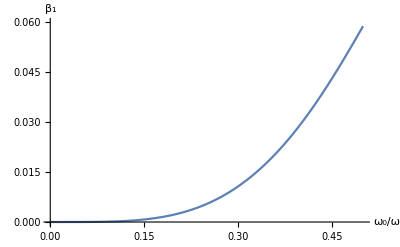

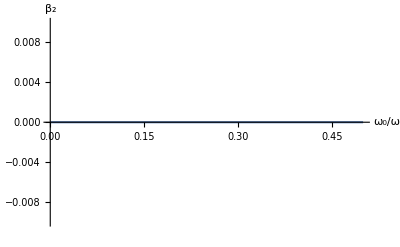

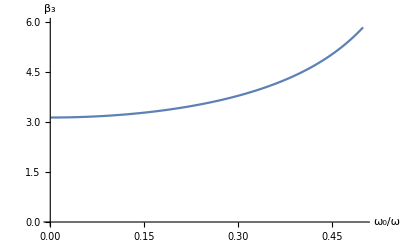

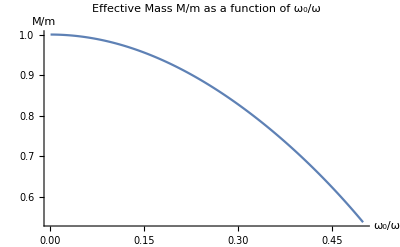

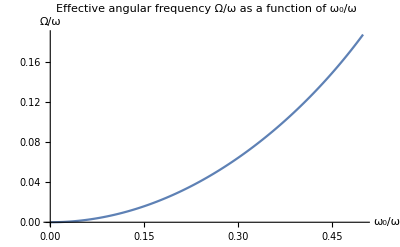

```mathematica
ListPlot[dataβ1,AxesLabel->{"ω_0/ω","β_1"},PlotRange->{0.0,0.06},Joined->True]
ListPlot[dataβ2,AxesLabel->{"ω_0/ω","β_2"},PlotRange->{-0.01,0.01},Joined->True]
ListPlot[dataβ3,AxesLabel->{"ω_0/ω","β_3"},PlotRange->{0,6.0},Joined->True]
ListPlot[dataM,AxesLabel->{"ω_0/ω","M/m"},PlotLabel->"Effective Mass M/m as a function of ω_0/ω",Joined->True]
ListPlot[dataΩ,AxesLabel->{"ω_0/ω","Ω/ω"},PlotLabel->"Effective angular frequency Ω/ω as a function of ω_0/ω",Joined->True]
```

### Numerical Solution

First we do some preliminary calculations.

```mathematica
vα=Table[Subscript[α,k1],{k1,1,n}];
Ma=LieGetMa[c,J,vα];
ν=LieGetNu[Ma,J];
νi=Inverse[ν];
```

To illustrate the numerical method we start by obtaining just one point of the effective Hamiltonian H_e for the quantum harmonic oscillator with time-dependent frequency (Paul trap). This means that the β parameters are calculated for one value of the mass (𝓂=1.0) and ω_0=2.0. As an example we have chosen ω = 4.0.

```mathematica
m=100;
𝓂=1.0;
ω0=2.0;
ω=10.0;
T=2π/ω
```

0.628319

We numerically solve (NDSolve) the time differential euqtions difeqst for the α parameters obtained above for 𝓂=1.0, ω_0=10.0 and ω = 4.0.

```mathematica
vαt=Table[Subscript[α,k1][t],{k1,1,n}];
difeqstn=difeqst/.{Subscript[a, 1]->𝓂/2 ω0^2 Cos[ω t],Subscript[a, 2]->0,Subscript[a, 3]->1/(2𝓂)};
solt=NDSolve[difeqstn,vαt,{t,0,T}][[1]];
```

The solution is then used to obtain α(T), the α parameters evaluated in T.

```mathematica
vαT=vαt/.solt/.{t->T}
```

{0.0234735,-0.00795757,0.344456}

To simplify the calculation we find the eigenvalue one eigenvectors of  M_a^⊤ evaluated in α(T). We use the eigenvalues and eigenvectors calculated in the previous section. To avoid divergencies we multiply the eigenvectors by α_3

```mathematica
evaln=eval[[1]]/.Table[vα[[k1]]->vαT[[k1]],{k1,1,n}]
evecn=Subscript[α, 3] evec[[1]]/.Table[vα[[k1]]->vαT[[k1]],{k1,1,n}];
ρ=evecn
```

1

{0.0234735,1.05328×10^-8,0.344456}

We calculate α as a function of β using Eq. (103) and verify that the condition (104) is met.
The inverse function in Eq. (18) is calculated by finding the minimum of the χ function for α(T)

```mathematica
χ[γ_]:=Norm[vαT-LieGetNAlpha[J,νi,vα,γ ρ,m]]^2;
γ=Sort[Table[{γ,χ[γ]},{γ,0.45,1.01,0.0005}],#1[[2]]<#2[[2]]&][[1]]
vβN=γ[[1]] ρ
```

{0.9895,7.19231×10^-9}

{0.023227,1.04222×10^-8,0.340839}

Therefore, for ω=10.0 we have β_1=0.023227, β_2=0.0 and β_3=0.340839. To test the numerical solution we can compare it with the previously obtained exact solutions for Ω/ω and M/m as functions of ω_0/ω .

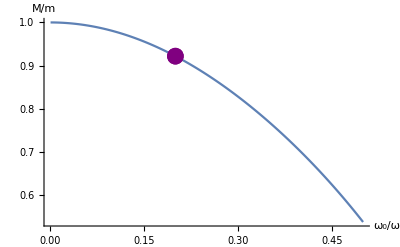

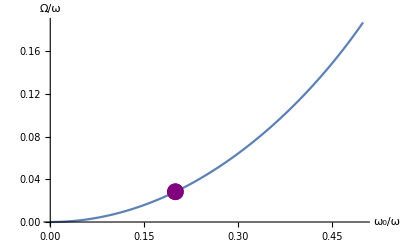

```mathematica
ListPlot[{dataM,{{ω0/ω,π/(𝓂 ω vβN[[3]])}}},PlotStyle->{Automatic,Directive[PointSize[0.03],Purple]},Joined->{True,False},AxesLabel->{"ω_0/ω","M/m"}]
ListPlot[{dataΩ,{{ω0/ω,1/π √(vβN[[1]]vβN[[3]])}}},PlotStyle->{Automatic,Directive[PointSize[0.03],Purple]},Joined->{True,False},AxesLabel->{"ω_0/ω","Ω/ω"}]
```

The reader may change the value of the parameter ω and repeat the calculation to verify that the numerical solution is consisten with the exact one.
Now we add a loop to the procedure to calculate the effective Hamiltonian for various values of the parameter ω.

```mathematica
m=100;
𝓂=1.0;
ω0=2.0;
ωmin=5.0;
ωmax=35.0;
Δω=3.0;
dataNM={};
dataNΩ={};
prog=0.0;
ProgressIndicator[Dynamic[prog]]
Do[
prog=(ω-ωmin)/(ωmax-ωmin);
T=2π/ω;
vαt=Table[Subscript[α,k1][t],{k1,1,n}];
difeqstn=difeqst/.{Subscript[a, 1]->𝓂/2 ω0^2 Cos[ω t],Subscript[a, 2]->0,Subscript[a, 3]->1/(2𝓂)};
solt=NDSolve[difeqstn,vαt,{t,0,T}][[1]];
vαT=vαt/.solt/.{t->T};
evaln=eval[[1]]/.Table[vα[[k1]]->vαT[[k1]],{k1,1,n}];
evecn=Subscript[α, 3] evec[[1]]/.Table[vα[[k1]]->vαT[[k1]],{k1,1,n}];
ρ=evecn;
χ[γ_]:=Norm[vαT-LieGetNAlpha[J,νi,vα,γ ρ,m]]^2;
γ=Sort[Table[{γ,χ[γ]},{γ,0.45,1.01,0.0005}],#1[[2]]<#2[[2]]&][[1,1]];
vβN=γ ρ;
AppendTo[dataNM,{ω0/ω,π/(𝓂 ω vβN[[3]])}];
AppendTo[dataNΩ,{ω0/ω,1/π √(vβN[[1]]vβN[[3]])}];
,{ω,ωmin,ωmax,Δω}]
```

Superimposing the exact solution for Ω/ω and M/m as functions of ω_0/ω, to the numerical one, we obtain the following plot

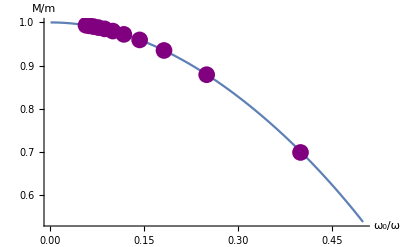

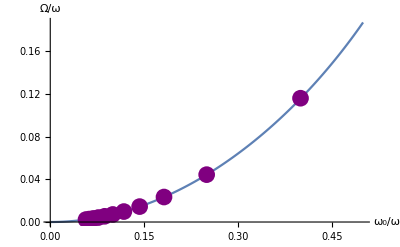

```mathematica
ListPlot[{dataM,dataNM},PlotStyle->{Automatic,Directive[PointSize[0.03],Purple]},Joined->{True,False},AxesLabel->{"ω_0/ω","M/m"}]
ListPlot[{dataΩ,dataNΩ},PlotStyle->{Automatic,Directive[PointSize[0.03],Purple]},Joined->{True,False},AxesLabel->{"ω_0/ω","Ω/ω"}]
```

We observe that the numerical solution for the effective Hamiltonian is identical to the exact one.